Приложение А.

```mathematica
Needs["Splines`"]
```

```mathematica
(*Введём начальные значения, по которым будем строить сплайн*)
```

```mathematica
n=3;
```

```mathematica
Uzl={0.1,0.3,0.7,1.4};
```

```mathematica
Znach={1,-7,15,25};
```

```mathematica
Do[{Subscript[x, i]=Uzl⟦i+1⟧,Subscript[f, i]=Znach⟦i+1⟧},{i,0,n}]
```

```mathematica
(*Построим линейный сплайн с дефектом 1 - Subscript[S, 1,1](x)*)
```

```mathematica
Subscript[P, k_][X_]=Subscript[f, k]+(X-Subscript[x, k])*Subscript[A, k];
```

```mathematica
(*Составим уравнение для нахождения коэффициентов*)
```

```mathematica
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
```

```mathematica
eq2={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
```

```mathematica
eq=Join[eq1,eq2];
```

```mathematica
(*Найдём их, подставив в исходные многочлены и построим график сплайна*)
```

```mathematica
koef = Solve[eq,{}]//Flatten
```

{A_0→-40.,A_1→55.,A_2→14.2857}

```mathematica
Spl[X_]=Table[Subscript[P, k][X]/.koef,{k,0,n-1}]//Expand
```

{5.-40. X,-23.5+55. X,5.+14.2857 X}

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}],PlotStyle->{PointSize[0.02]},
PlotRange->{{0,3},{-30,30}}];
```

```mathematica
Gr2=Table[Plot[Spl[X]⟦k⟧,{X,Subscript[x, k-1],Subscript[x, k]}],{k,1,n}];
```

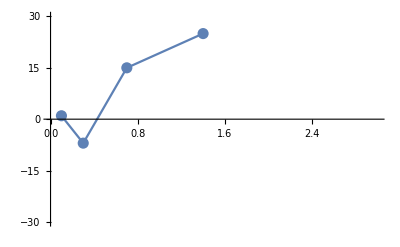

```mathematica
Show[Gr1,Gr2]
```